```mathematica
Rule2[g_,e_, e2_]:= Block[{new, result, start = e[[1]], stop=e[[2]], start2 = e2[[1]], stop2=e2[[2]]},
new=Max[VertexList[g]]+1;
result=EdgeDelete[g,e];
result=VertexAdd[result,new];
result=EdgeAdd[result,{start<->new,stop<->new,start2<->new,stop2<->new}];
result]
```

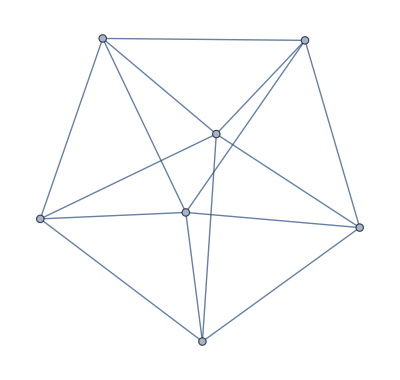
Rule2[-Graphics-,3<->6]

```mathematica
Rule2[ReadGrof[7],3<->6]
```

```mathematica
With[
{g=ReadGrof[7]},
Print[EdgeList[g]];
Select[VertexList[g],(MemberQ[EdgeList[g],#<->3 ] ||MemberQ[EdgeList[g],3<-># ])&& (MemberQ[EdgeList[g],6<-># ]||MemberQ[EdgeList[g],#<->6 ])&]
]
```

{1<->2,1<->3,1<->5,1<->7,2<->3,2<->5,2<->6,3<->4,3<->6,3<->7,4<->5,4<->6,4<->7,5<->6,5<->7}

{2,4}

```mathematica
MemberQ[{1<->2,1<->3,1<->5,1<->7,2<->3,2<->5,2<->6,3<->4,3<->6,3<->7,4<->5,4<->6,4<->7,5<->6,5<->7},2<->1 ]
```

False